## Задача 1. Дадено е уравнението: (√(x^3)-(1+a+b)sinx)/(1+cos^2 x)-3(a+b+2)=0, където a = 0, b = 3 Уравнението се превръща в: (√(x^3)- 4Sin[x])/(1+Cos[x]^2)-15=0.

## а) Да се намери общият брой на корените на уравнението - правим геометрична интерпретация на уравнението:

```mathematica
f[x_]:=(√(x^3)- 4Sin[x])/(1+Cos[x]^2)-15
```

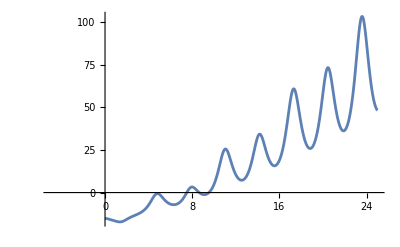

```mathematica
Plot[f[x],{x,-5,25}]
```

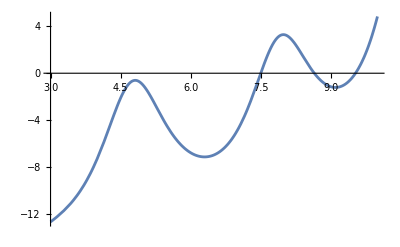

```mathematica
Plot[f[x],{x,3,10}]
```

Отговор: Уравнението има 3 реални корена, защото графиката на функцията пресича 3 пъти абцисната ос.

## б) Да се локализира най-големият реален корен в интервал [p;q].

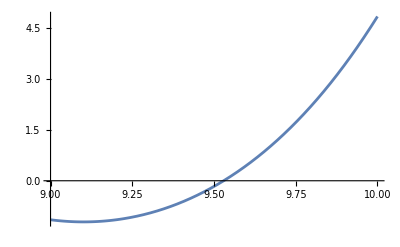

```mathematica
Plot[f[x],{x,9,10}]
```

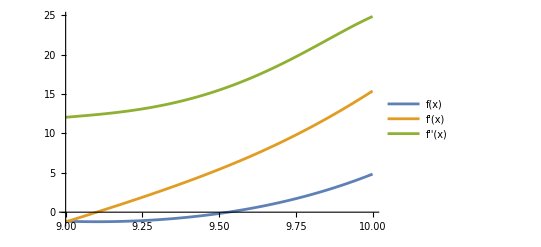

```mathematica
Plot[{f[x], f'[x], f''[x]}, {x, 9, 10}, PlotLegends->"Expressions"]
```

```mathematica
f[9.]
```

-1.14791

```mathematica
f[10.]
```

4.83453

Извод:
(1) Функцията f(x) е непрекъсната, защото е сума от непрекъснати функции 
(2). f(9) =  -1.1479... < 0 
 f(10) =  4.8345... > 0
Функцията има различни знаци в двата края на разглеждания интервал [9; 10].
Следователно от (1) и (2) следва, че в интервала [9; 10] функцията има поне един корен.

## в) Да се направят 4 итерации по метода на разполовяването за интервала [p;q]. Представете таблица с изчисленията.

```mathematica
f[x_]:=(√(x^3)- 4Sin[x])/(1+Cos[x]^2)-15
a = 9.;
b = 10.;
For[n = 0, n<= 4, n++,
Print["n = ",n, " a = ",a, " b = ",b, " m = ",m = (a+b)/2, " f(m) = ",f[m], " ε = ",(b-a)/2];
If[f[m]<0,a=m,b=m]
]
```

n = 0 a = 9. b = 10. m = 9.5 f(m) = -0.167329 ε = 0.5

n = 1 a = 9.5 b = 10. m = 9.75 f(m) = 1.71443 ε = 0.25

n = 2 a = 9.5 b = 9.75 m = 9.625 f(m) = 0.63744 ε = 0.125

n = 3 a = 9.5 b = 9.625 m = 9.5625 f(m) = 0.203045 ε = 0.0625

n = 4 a = 9.5 b = 9.5625 m = 9.53125 f(m) = 0.0100822 ε = 0.03125

Отговор:

n = 1 a = 9.5 b = 10. m = 9.75 f(m) = 1.71443 ε = 0.25

n = 2 a = 9.5 b = 9.75 m = 9.625 f(m) = 0.63744 ε = 0.125

n = 3 a = 9.5 b = 9.625 m = 9.5625 f(m) = 0.203045 ε = 0.0625

n = 4 a = 9.5 b = 9.5625 m = 9.53125 f(m) = 0.0100822 ε = 0.03125

## г) Посочете достигнатото приближение и с каква точност е то.

Отговор: На четвъртата итерация приближеното решение е 9.53125 с грешка 0.03125.

## д) Колко итерации биха били нужни за достигане на точност ε = 0,0000001.

```mathematica
Log2[(10-9)/0.0000001]-1
```

22.2535

Отговор: Най-малкото цяло число, което е по-голямо от 22.2535 е 23. Следователно са необходими минимум 23 итерации за достигане на исканата точност 0,0000001.

## е) Може ли за избрания интервал да се приложи метода на Нютон? Обосновете отговора си.

### Проверка на знака на първата производна

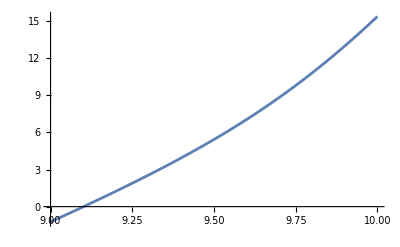

```mathematica
Plot[f'[x], {x,9,10}]
```

Извод: (1) Първата производна си сменя знака в интервала [9; 10].

### Проверка на знака на втората производна

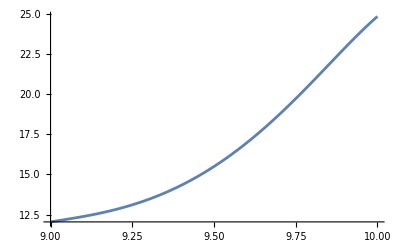

```mathematica
Plot[f''[x], {x,9,10}]
```

Извод: (2) Втората производна има стойности между 12 и 25. Следователно те са изцяло положителни и f’’(x) > 0 за целия интервал [9; 10].

Отговор: От (1) и (2) следва, че не са изпълнени условията на метода на Нютон, тъй като първата производна си сменя знака в интервала [9;10], докато втората производна има постоянен знак в целия интервал.